```mathematica
ClearAll["Global`*"]
<<MaTeX`
```

### Heliconical ground state drawing

```mathematica
c2 [a_]:= (1 + 2a) - (4 a (1+a))^(1/2)
q[x_,y_]:=2y((1+2x)- (4x(1+x))^(1/2))/Sqrt[1 - ((1+2x)- (4x(1+x))^(1/2))^2]
x[θ_,q_] := Sin[θ]^4/Cos[2θ]
y[θ_,q_] := q Tan[θ]/2
theta[x_,y_]:=1/2 ArcCos[(1+2x)- (4x(1+x))^(1/2)]
bendmag[x_,y_]:= y((1+2x)- (4x(1+x))^(1/2))
```

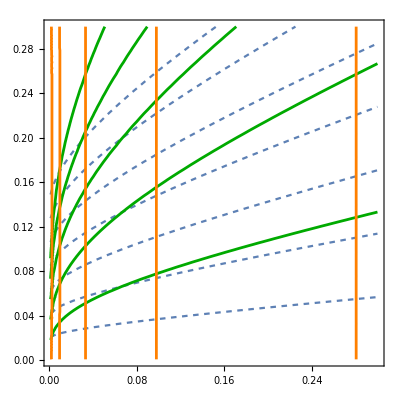

```mathematica
lower = 0.001;
upper = 0.3;
qcontours={0.1,0.2,0.3, 0.4,0.5};
qg = ContourPlot[q[x,y]==qcontours,{x,lower,upper},{y,lower,upper}
,ContourLabels->True
,ContourStyle->Directive[Darker[Green],Thickness[0.005]]
];

thetacontours={0.2,0.3,0.4,0.5,0.6};
thetag = ContourPlot[theta[x,y]==thetacontours,{x,lower,upper},{y,lower,upper}
	,ContourStyle->Directive[Orange,Thickness[0.005]]
	,ContourLabels->True];

bendcontours={0.02,0.04,0.06,0.08, 0.1,0.12,0.14};
bendmagg=ContourPlot[bendmag[x,y]==bendcontours,{x,lower,upper},{y,lower,upper}
,PlotLegends->Automatic
,ContourStyle->Directive[AbsoluteDashing[4]]
,BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->11}
, FrameLabel ->{MaTeX@"C/K",MaTeX@"\lambda/K"}
,FrameStyle->Black
];
Show[bendmagg,qg,thetag]
```

```mathematica
Some example Helices
```

```mathematica
r[t_,θ_,q_]:={1/q Tan[θ]Sin[q t],1/q Tan[θ]Cos[q t],t}
```

```mathematica
xvalues ={0.05,0.1,0.15,0.2};
yvalue = 0.15;
lims = 2π/yvalue;
s={1,1,1,1};
colours={Red,Blue,Orange,Green };
For[i=0,i<=4,i++,
	s[[i]]=ParametricPlot3D[r[t,theta[xvalues[[i]],yvalue],q[xvalues[[i]],yvalue]]
,{t,-lims,lims}
,PlotStyle->{colours[[i]],Thickness[0.015]}
];
]
Show[s[[4]],s[[3]],s[[2]],s[[1]],Boxed->False,Axes->False,ViewPoint->10{0.2,0.2,1}]
```

-Graphics3D-

```mathematica
yvalues ={0.05,0.1,0.15,0.2};
xvalue = 0.15;
lims = 2π/yvalues;
s={1,1,1,1};
colours={Red,Blue,Orange,Green};
For[i=1,i<=4,i++,
	s[[i]]=ParametricPlot3D[r[t,theta[xvalue,yvalues[[i]]],q[xvalue,yvalues[[i]]]]
,{t,-70,70}
,PlotStyle->{colours[[i]],Thickness[0.015]}];
]
Show[s[[1]],s[[2]],s[[3]],s[[4]],Boxed->False,Axes->False,ViewPoint->8{0.2,0.2,1}]
```

-Graphics3D-